# Comparison of Collimated Flux Methods

## Units + Constants

```mathematica
(*Units*)
MeV=10^6;
keV=10^3;
nC=10^-9;
pC=10^-12;
μJ=10^-6;
nm=10^-9;
mrad=10^-3;
mm=10^-3;
cm=10^-2;
μm=10^-6;
MHz=10^6;
```

```mathematica
(*Constants*)
σT=6.65245871548*10^-29;
re=2.8179403262*10^-15;
clight=299792458;
hbar=6.5821*10^-16; (*converted to eV, wavelength calc changed accordingly*)
me=0.51099895MeV; (*mc^2 really*)
elecharge=1.60217662*10^-19;
```

## Plotting

```mathematica
frame[legend_]:=Framed[legend,FrameStyle->Black,RoundingRadius->0,FrameMargins->0]
```

## Cases

```mathematica
headonCBETA150={Ee->150MeV,λ->1064nm,Q->32pC,Epulse->62μJ,βIP->1cm,ϵn->0.3mm mrad,σL->25μm,f->162.5MHz,θcol->0.5mrad};
headonCBETA150opt={Ee->150MeV,λ->1064nm,Q->32pC,Epulse->62μJ,βIP->12.6189cm,ϵn->0.3mm mrad,σL->25μm,f->162.5MHz,θcol->0.43333mrad};

headonDIANA687={Ee->687MeV,λ->1064nm,Q->100pC,Epulse->100μJ,βIP->0.2,ϵn->0.5mm mrad,σL->25 μm,f->100MHz,θcol->0.1mrad};
headonDIANA687opt={Ee->687MeV,λ->1064nm,Q->100pC,Epulse->100μJ,βIP->0.603575,ϵn->0.5mm mrad,σL->25 μm,f->100MHz,θcol->0.09181mrad};
```

## Intermediaries

```mathematica
(*Scattered photon energy equations*) 
γ[Ee_]:=(Ee+me)/me;
β[Ee_]:=Sqrt[1-1/γ[Ee]^2];
EL[λ_]:=(2*π*hbar*clight)/λ; (*in eV, using hbar*)
Xrec[Ee_,λ_]:=(4*γ[Ee]*EL[λ])/me;
(*Photon production equations*)
σc[Ee_,λ_]:=σT*(1-Xrec[Ee,λ]);
Ne[Q_]:=Q/elecharge;
NL[Epulse_,λ_]:=Epulse/(elecharge*EL[λ]);
σe[βIP_,ϵn_,Ee_]:=Sqrt[(βIP*ϵn)/γ[Ee]];
zr[σL_,λ_]:=(4*π*σL^2)/λ;
σzl[tpulse_]:=clight*tpulse;
convxy[βIP_,ϵn_,Ee_,σL_]:=Sqrt[σe[βIP,ϵn,Ee]^2+σL^2];
convz[σze_,tpulse_]:=Sqrt[σze^2+σzl[tpulse]^2];
(*Collimation Equations*)
ψ[Ee_,θ_]:=γ[Ee]*θ;
```

## Scattered Photon Energy + Mandelstam Y Variable

```mathematica
Eγ[Ee_,λ_,θ_]:=(4*γ[Ee]^2*EL[λ])/(1+γ[Ee]^2*θ^2+Xrec[Ee,λ]);
```

```mathematica
Y[Ee_,λ_,θ_]:=(2*γ[Ee]*Eγ[Ee,λ,θ]*(1-β[Ee]*Cos[θ]))/me;
```

## Luminosity

```mathematica
L[Ee_,λ_,Q_,Epulse_,βIP_,ϵn_,σL_]:=(Ne[Q]*NL[Epulse,λ])/(2*π*convxy[βIP,ϵn,Ee,σL]^2);
```

## Curatolo F_ψ Method

```mathematica
FψCuratolo[Ee_,λ_,Q_,Epulse_,βIP_,ϵn_,σL_,f_,θ_]:=σc[Ee,λ]*L[Ee,λ,Q,Epulse,βIP,ϵn,σL]*f*((1+(CubeRoot[Xrec[Ee,λ]]*ψ[Ee,θ]^2)/3)*ψ[Ee,θ]^2)/((1+(1+Xrec[Ee,λ]/2)ψ[Ee,θ]^2)*(1+ψ[Ee,θ]^2));
```

```mathematica
FψCuratolo[Ee,λ,Q,Epulse,βIP,ϵn,σL,f,θcol]/.headonCBETA150
```

3.72655×10^9

```mathematica
FψCuratolo[Ee,λ,Q,Epulse,βIP,ϵn,σL,f,θcol]/.headonCBETA150opt
```

2.38398×10^9

```mathematica
FψCuratolo[Ee,λ,Q,Epulse,βIP,ϵn,σL,f,θcol]/.headonDIANA687
```

8.74197×10^9

```mathematica
FψCuratolo[Ee,λ,Q,Epulse,βIP,ϵn,σL,f,θcol]/.headonDIANA687opt
```

6.10023×10^9

## Krafft F_(0.1%) Method

```mathematica
F01[Ee_,λ_,Q_,Epulse_,βIP_,ϵn_,σL_,f_]:=1.5*10^-3*σc[Ee,λ]*L[Ee,λ,Q,Epulse,βIP,ϵn,σL]*f;
```

```mathematica
F01[Ee,λ,Q,Epulse,βIP,ϵn,σL,f]/.headonCBETA150
```

2.68767×10^8

```mathematica
F01[Ee,λ,Q,Epulse,βIP,ϵn,σL,f]/.headonCBETA150opt
```

2.26557×10^8

```mathematica
F01[Ee,λ,Q,Epulse,βIP,ϵn,σL,f]/.headonDIANA687
```

7.49906×10^8

```mathematica
F01[Ee,λ,Q,Epulse,βIP,ϵn,σL,f]/.headonDIANA687opt
```

6.17479×10^8

## Cross Section Integral Method (Based on Sun Calc)

```mathematica
dσdθ[Ee_,λ_,θ_]:=(16*π*re^2)/Xrec[Ee,λ]^2*((1/Xrec[Ee,λ]-1/Y[Ee,λ,θ])^2+1/Xrec[Ee,λ]-1/Y[Ee,λ,θ]+1/4*(Xrec[Ee,λ]/Y[Ee,λ,θ]+Y[Ee,λ,θ]/Xrec[Ee,λ]))*(Eγ[Ee,λ,θ]/me)^2*Sin[θ];
```

```mathematica
Off[NIntegrate::inumr,NIntegrate::nlim];
```

```mathematica
σ[Ee_,λ_,θcol_]:=NIntegrate[dσdθ[Ee,λ,θ],{θ,0,θcol}];
```

```mathematica
σ[Ee,λ,θcol]/.headonCBETA150
```

2.05872×10^-30

```mathematica
σ[Ee,λ,θcol]/.headonDIANA687
```

1.70147×10^-30

```mathematica
CBETAσvsθ=Table[{θ/mrad,σ[Ee,λ,θ]/.headonCBETA150},{θ,0,1/γ[Ee]/.headonCBETA150,1/(1000*γ[Ee])/.headonCBETA150}];
```

```mathematica
DIANAσvsθ=Table[{θ/mrad,σ[Ee,λ,θ]/.headonDIANA687},{θ,0,1/γ[Ee]/.headonDIANA687,1/(1000*γ[Ee])/.headonDIANA687}];
```

```mathematica
CBETAColAngCrossSec=ListLinePlot[Partition[Riffle[CBETAσvsθ⟦All,1⟧,CBETAσvsθ⟦All,2⟧],2],Frame->True,LabelStyle->{15,FontFamily->"Calibri",FontColor->Black},PlotLabel->"CBETA 150 MeV",FrameLabel->{"Collimation Angle θ_col [mrad]","Int. Cross Section σ(θ_col) [m^2]"},ImageSize->Medium];
DIANAColAngCrossSec=ListLinePlot[Partition[Riffle[DIANAσvsθ⟦All,1⟧,DIANAσvsθ⟦All,2⟧],2],Frame->True,LabelStyle->{15,FontFamily->"Calibri",FontColor->Black},PlotLabel->"DIANA 687 MeV",FrameLabel->{"Collimation Angle θ_col [mrad]","Int. Cross Section σ(θ_col) [m^2]"},ImageSize->Medium];
```

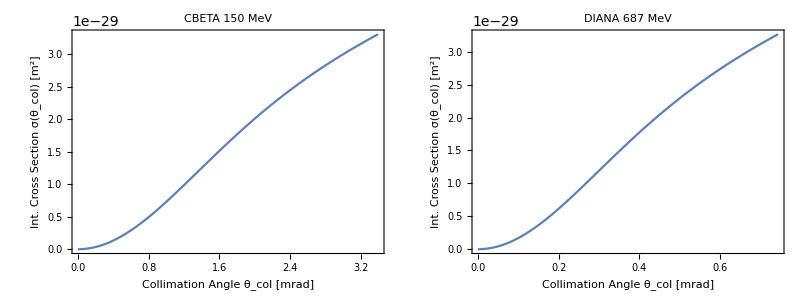

```mathematica
Grid[{{CBETAColAngCrossSec,DIANAColAngCrossSec}}]
```

## Collimated Flux Integral Method (Based on Sun Calc)

```mathematica
Fcol[Ee_,λ_,θcol_,Q_,Epulse_,βIP_,ϵn_,σL_,f_]:=σ[Ee,λ,θcol]*L[Ee,λ,Q,Epulse,βIP,ϵn,σL]*f;
```

## CBETA Collimated Flux Comparison (Sun Integral vs Curatolo)

```mathematica
CBETAFcolvsθ=Table[{θ/mrad,Fcol[Ee,λ,θ,Q,Epulse,βIP,ϵn,σL,f]/.headonCBETA150,FψCuratolo[Ee,λ,Q,Epulse,βIP,ϵn,σL,f,θ]/.headonCBETA150},{θ,0,1/γ[Ee]/.headonCBETA150,1/(1000*γ[Ee])/.headonCBETA150}];
```

```mathematica
CBETAFcolvsθopt=Table[{θ/mrad,Fcol[Ee,λ,θ,Q,Epulse,βIP,ϵn,σL,f]/.headonCBETA150opt,FψCuratolo[Ee,λ,Q,Epulse,βIP,ϵn,σL,f,θ]/.headonCBETA150opt},{θ,0,1/γ[Ee]/.headonCBETA150opt,1/(1000*γ[Ee])/.headonCBETA150opt}];
```

```mathematica
CBETAFcol=ListLinePlot[{Partition[Riffle[CBETAFcolvsθ⟦All,1⟧,CBETAFcolvsθ⟦All,2⟧],2],Partition[Riffle[CBETAFcolvsθ⟦All,1⟧,CBETAFcolvsθ⟦All,3⟧],2]},Frame->True,LabelStyle->{15,FontFamily->"Calibri",FontColor->Black},PlotLabel->"Baseline Configuration",FrameLabel->{"Collimation Angle θ_col [mrad]","Collimated Flux F_col [ph/s]"},PlotLegends->Placed[LineLegend[{"Sun Integral","Curatolo Analytical (No Corr Fac)"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.3,0.8}],PlotRange->Full,ImageSize->Large];
```

```mathematica
optCBETAFcol=ListLinePlot[{Partition[Riffle[CBETAFcolvsθopt⟦All,1⟧,CBETAFcolvsθopt⟦All,2⟧],2],Partition[Riffle[CBETAFcolvsθopt⟦All,1⟧,CBETAFcolvsθopt⟦All,3⟧],2]},Frame->True,LabelStyle->{15,FontFamily->"Calibri",FontColor->Black},PlotLabel->"Optimised 0.5% Bandwidth Configuration",FrameLabel->{"Collimation Angle θ_col [mrad]","Collimated Flux F_col [ph/s]"},PlotLegends->Placed[LineLegend[{"Sun Integral","Curatolo Analytical (No Corr Fac)"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.3,0.8}],PlotRange->Full,ImageSize->Large];
```

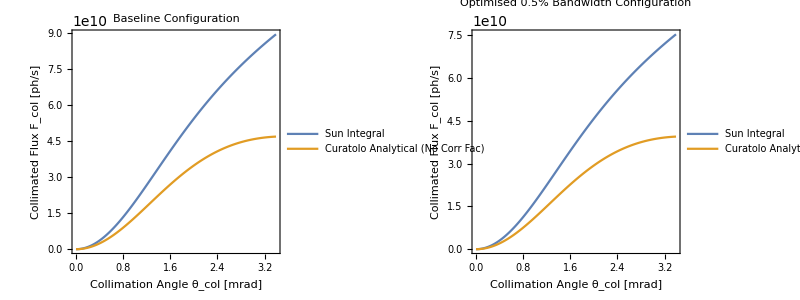

```mathematica
Grid[{{CBETAFcol,optCBETAFcol}}]
```

## DIANA Collimated Flux Comparison (Sun Integral vs Curatolo)

```mathematica
DIANAFcolvsθ=Table[{θ/mrad,Fcol[Ee,λ,θ,Q,Epulse,βIP,ϵn,σL,f]/.headonDIANA687,FψCuratolo[Ee,λ,Q,Epulse,βIP,ϵn,σL,f,θ]/.headonDIANA687},{θ,0,1/γ[Ee]/.headonDIANA687,1/(1000*γ[Ee])/.headonDIANA687}];
```

```mathematica
DIANAFcolvsθopt=Table[{θ/mrad,Fcol[Ee,λ,θ,Q,Epulse,βIP,ϵn,σL,f]/.headonDIANA687opt,FψCuratolo[Ee,λ,Q,Epulse,βIP,ϵn,σL,f,θ]/.headonDIANA687opt},{θ,0,1/γ[Ee]/.headonDIANA687opt,1/(1000*γ[Ee])/.headonDIANA687opt}];
```

```mathematica
DIANAFcol=ListLinePlot[{Partition[Riffle[DIANAFcolvsθ⟦All,1⟧,DIANAFcolvsθ⟦All,2⟧],2],Partition[Riffle[DIANAFcolvsθ⟦All,1⟧,DIANAFcolvsθ⟦All,3⟧],2]},Frame->True,LabelStyle->{15,FontFamily->"Calibri",FontColor->Black},PlotLabel->"Baseline Configuration",FrameLabel->{"Collimation Angle θ_col [mrad]","Collimated Flux F_col [ph/s]"},PlotLegends->Placed[LineLegend[{"Sun Integral","Curatolo Analytical (No Corr Fac)"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.3,0.8}],PlotRange->Full,ImageSize->Large];
```

```mathematica
optDIANAFcol=ListLinePlot[{Partition[Riffle[DIANAFcolvsθopt⟦All,1⟧,DIANAFcolvsθopt⟦All,2⟧],2],Partition[Riffle[DIANAFcolvsθopt⟦All,1⟧,DIANAFcolvsθopt⟦All,3⟧],2]},Frame->True,LabelStyle->{15,FontFamily->"Calibri",FontColor->Black},PlotLabel->"Optimised 0.5% Bandwidth Configuration",FrameLabel->{"Collimation Angle θ_col [mrad]","Collimated Flux F_col [ph/s]"},PlotLegends->Placed[LineLegend[{"Sun Integral","Curatolo Analytical (No Corr Fac)"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.3,0.8}],PlotRange->Full,ImageSize->Large];
```

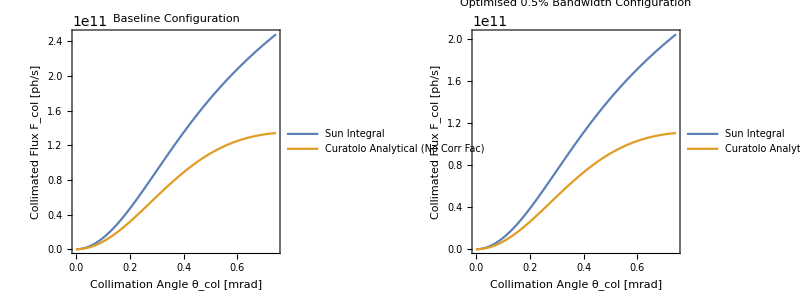

```mathematica
Grid[{{DIANAFcol,optDIANAFcol}},ItemSize->Automatic]
```

## Baseline vs Optimised Collimated Flux Integral Method (Based on Sun Calc) Comparison

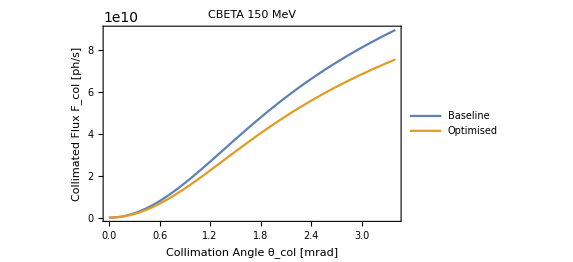

```mathematica
ListLinePlot[{Partition[Riffle[CBETAFcolvsθ⟦All,1⟧,CBETAFcolvsθ⟦All,2⟧],2],Partition[Riffle[CBETAFcolvsθopt⟦All,1⟧,CBETAFcolvsθopt⟦All,2⟧],2]},Frame->True,LabelStyle->{15,FontFamily->"Calibri",FontColor->Black},PlotLabel->"CBETA 150 MeV",FrameLabel->{"Collimation Angle θ_col [mrad]","Collimated Flux F_col [ph/s]"},PlotLegends->Placed[LineLegend[{"Baseline","Optimised"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.3,0.8}]]
```

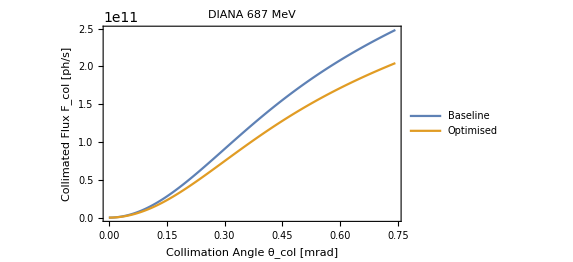

```mathematica
ListLinePlot[{Partition[Riffle[DIANAFcolvsθ⟦All,1⟧,DIANAFcolvsθ⟦All,2⟧],2],Partition[Riffle[DIANAFcolvsθopt⟦All,1⟧,DIANAFcolvsθopt⟦All,2⟧],2]},Frame->True,LabelStyle->{15,FontFamily->"Calibri",FontColor->Black},PlotLabel->"DIANA 687 MeV",FrameLabel->{"Collimation Angle θ_col [mrad]","Collimated Flux F_col [ph/s]"},PlotLegends->Placed[LineLegend[{"Baseline","Optimised"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.3,0.8}]]
```

## ICARUS Integrated Flux - [ADD DIANA 687 MeV RUN]

```mathematica
SetDirectory["C:/Users/user/Documents/Wolfram Mathematica/ICARUS_data/CBETA"];
CBETA150N200M=<<"CBETA150_200mil.txt";
```

Note that the ICARUS data here isn’t exactly optimised for the head-on case , it is for a 5° crossing angle.

```mathematica
CBETAoptICARUSIntFlux=Integrate[Interpolation[CBETA150N200M][x],{x,Min[CBETA150N200M⟦All,1⟧],Max[CBETA150N200M⟦All,1⟧]}]*f*Q/nC/.headonCBETA150
```

3.45231×10^9

```mathematica
SetDirectory["C:/Users/user/Documents/Wolfram Mathematica/ICARUS_data/DIANA/7MeV_15MVm"];
DIANA687N100M=<<"DIANA687_100M.txt";
```

```mathematica
DIANAoptICARUSIntFlux=Integrate[Interpolation[DIANA687N100M][x],{x,Min[DIANA687N100M⟦All,1⟧],Max[DIANA687N100M⟦All,1⟧]}]*f*Q/nC/.headonDIANA687opt
```

8.75747×10^9

## ICCS3D Integrated Flux - [NEED TO ASK BALSA TO DO A DIANA 687 MeV RUN]

Note that the ICCS3D data here isn’t exactly optimised for the head-on case , it is for a 5° crossing angle.

```mathematica
rawdata=Import["C:/Users/user/Documents/Wolfram Mathematica/ICARUS_data/CBETA/CBETA150_ICCS3D_FINAL.txt","Words"];
ndata=Length[rawdata];
ncolumns=6;
ndat=ndata/ncolumns;
BalsaICCS=Array[Ω,{2,ndat}];
For[i=0,i<(ndat+1),i++,
(*for energy*)
Ω[1,i]=Interpreter["Number"][ToString[rawdata⟦1+ncolumns*(i-1)⟧]]*10^-3;
(*for specden*)
Ω[2,i]=Interpreter["Number"][ToString[rawdata⟦3+ncolumns*(i-1)⟧]]*(keV*nC)/elecharge;
];
BalsaVals=Array[Υ,{2,0}];
For[i=1,i<Length[Transpose[BalsaICCS]]+1,i++,
If[BalsaICCS⟦2,i⟧>10^-20,
AppendTo[BalsaVals⟦1⟧,BalsaICCS⟦1,i⟧];
AppendTo[BalsaVals⟦2⟧,BalsaICCS⟦2,i⟧];
];
];
```

```mathematica
BalsaVals=Transpose[BalsaVals];
```

```mathematica
CBETAoptICCS3DIntFlux=Integrate[Interpolation[BalsaVals][x],{x,Min[BalsaVals⟦All,1⟧],Max[BalsaVals⟦All,1⟧]}]*f*Q/nC/.headonCBETA150
```

3.57972×10^9

## Table of Methods

This is the comparative table of methods for the collimated flux calculations and their differences. These are all calculated head-on as I haven’t yet determined if R_AC is a suitable method or if this can be derived into Sun’s cross section/ Mandelstam variables. The Krafft calculation is done via F_(0.5%) ≃ 5 F_(0.1%) which is a good approximation.

```mathematica
Grid[{{"CBETA 150 MeV Fluxes",SpanFromLeft,SpanFromLeft,SpanFromLeft,SpanFromLeft,SpanFromLeft,SpanFromLeft,"CBETA 150 MeV Flux Differences",SpanFromLeft,SpanFromLeft},{"Flux Case","Sun Integral","Curatolo Analytical","Krafft Analytical","ICCS3D","ICARUS","Units","F_SUN/F_CURATOLO","F_SUN/F_KRAFFT","F_CURATOLO/F_KRAFFT"},{"0.5% BW Optimised",Fcol[Ee,λ,θcol,Q,Epulse,βIP,ϵn,σL,f]/.headonCBETA150opt,FψCuratolo[Ee,λ,Q,Epulse,βIP,ϵn,σL,f,θcol]/.headonCBETA150opt,5*F01[Ee,λ,Q,Epulse,βIP,ϵn,σL,f]/.headonCBETA150opt,CBETAoptICCS3DIntFlux,CBETAoptICARUSIntFlux,"ph/s",Fcol[Ee,λ,θcol,Q,Epulse,βIP,ϵn,σL,f]/FψCuratolo[Ee,λ,Q,Epulse,βIP,ϵn,σL,f,θcol]/.headonCBETA150opt,Fcol[Ee,λ,θcol,Q,Epulse,βIP,ϵn,σL,f]/(5*F01[Ee,λ,Q,Epulse,βIP,ϵn,σL,f])/.headonCBETA150opt,FψCuratolo[Ee,λ,Q,Epulse,βIP,ϵn,σL,f,θcol]/(5*F01[Ee,λ,Q,Epulse,βIP,ϵn,σL,f])/.headonCBETA150opt},{"Baseline",Fcol[Ee,λ,θcol,Q,Epulse,βIP,ϵn,σL,f]/.headonCBETA150,FψCuratolo[Ee,λ,Q,Epulse,βIP,ϵn,σL,f,θcol]/.headonCBETA150, "-","-","-","ph/s",Fcol[Ee,λ,θcol,Q,Epulse,βIP,ϵn,σL,f]/FψCuratolo[Ee,λ,Q,Epulse,βIP,ϵn,σL,f,θcol]/.headonCBETA150,"-","-"},{"DIANA 687 MeV Fluxes",SpanFromLeft,SpanFromLeft,SpanFromLeft,SpanFromLeft,SpanFromLeft,SpanFromLeft,"DIANA 687 MeV Flux Differences",SpanFromLeft,SpanFromLeft},{"Flux Case","Sun Integral","Curatolo Analytical","Krafft Analytical","ICCS3D","ICARUS","Units","F_SUN/F_CURATOLO","F_SUN/F_KRAFFT","F_CURATOLO/F_KRAFFT"},{"0.5% BW Optimised",Fcol[Ee,λ,θcol,Q,Epulse,βIP,ϵn,σL,f]/.headonDIANA687opt,FψCuratolo[Ee,λ,Q,Epulse,βIP,ϵn,σL,f,θcol]/.headonDIANA687opt,5*F01[Ee,λ,Q,Epulse,βIP,ϵn,σL,f]/.headonDIANA687opt,"data needed",DIANAoptICARUSIntFlux,"ph/s",Fcol[Ee,λ,θcol,Q,Epulse,βIP,ϵn,σL,f]/FψCuratolo[Ee,λ,Q,Epulse,βIP,ϵn,σL,f,θcol]/.headonDIANA687opt,Fcol[Ee,λ,θcol,Q,Epulse,βIP,ϵn,σL,f]/(5*F01[Ee,λ,Q,Epulse,βIP,ϵn,σL,f])/.headonDIANA687opt,FψCuratolo[Ee,λ,Q,Epulse,βIP,ϵn,σL,f,θcol]/(5*F01[Ee,λ,Q,Epulse,βIP,ϵn,σL,f])/.headonDIANA687opt},{"Baseline",Fcol[Ee,λ,θcol,Q,Epulse,βIP,ϵn,σL,f]/.headonDIANA687,FψCuratolo[Ee,λ,Q,Epulse,βIP,ϵn,σL,f,θcol]/.headonDIANA687, "-","-","-","ph/s",Fcol[Ee,λ,θcol,Q,Epulse,βIP,ϵn,σL,f]/FψCuratolo[Ee,λ,Q,Epulse,βIP,ϵn,σL,f,θcol]/.headonDIANA687,"-","-"}},Dividers->{{True,True,True,True,True,True,True,True,True,True,True},{True,True,True,False,True,True,True,False,True}}]
```

CBETA 150 MeV Fluxes |  |  |  |  |  |  | CBETA 150 MeV Flux Differences |  | 
Flux Case | Sun Integral | Curatolo Analytical | Krafft Analytical | ICCS3D | ICARUS | Units | F_SUN/F_CURATOLO | F_SUN/F_KRAFFT | F_CURATOLO/F_KRAFFT
0.5% BW Optimised | 3.55711×10^9 | 2.38398×10^9 | 1.13278×10^9 | 3.57972×10^9 | 3.45231×10^9 | ph/s | 1.49209 | 3.14015 | 2.10453
Baseline | 5.55991×10^9 | 3.72655×10^9 | - | - | - | ph/s | 1.49197 | - | -
DIANA 687 MeV Fluxes |  |  |  |  |  |  | DIANA 687 MeV Flux Differences |  | 
Flux Case | Sun Integral | Curatolo Analytical | Krafft Analytical | ICCS3D | ICARUS | Units | F_SUN/F_CURATOLO | F_SUN/F_KRAFFT | F_CURATOLO/F_KRAFFT
0.5% BW Optimised | 9.03451×10^9 | 6.10023×10^9 | 3.0874×10^9 | data needed | 8.75747×10^9 | ph/s | 1.48101 | 2.92626 | 1.97585
Baseline | 1.29456×10^10 | 8.74197×10^9 | - | - | - | ph/s | 1.48085 | - | -